```mathematica
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
inpath=NotebookDirectory[]<>"~salience\\";
outpath=NotebookDirectory[]<>"~saliencemap\\";
```

```mathematica
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,featurefilename,resultxml,imagefile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
chartcolors=rgbcolors[[#]]&/@index;
```

```mathematica
d = Import[volumefile,"Image3D"];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
imgs=Image3D[#,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]&/@Prepend[ImageMultiply[d,#]&/@features,d]//Image@Rasterize[#]&/@#&;
mixed=First@imgs;
imglist=imgs[[2;;]];
Export[imagefile,mixed];
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],#]&,imglist];
{mixed,imglist}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
ImageListAdd[imgs_]:=Module[{r},
r=First@imgs;
Table[r=ImageAdd[r,i],{i,imgs[[2;;]]}];
r
]
ImageListMultiply[imgs_]:=Module[{r},
r=First@imgs;
Table[r=ImageMultiply[r,i],{i,imgs[[2;;]]}];
r
]
ImageListSubtract[img_,imgs_]:=Module[{r},
r=img;
Table[r=ImageSubtract[r,i],{i,imgs}];
r
]
Compute2DFS[mixed_,imglist_]:=Module[{dist,n,sets,subsets,denominator,weights,saliency,overlap,size,left,gaussian,sumOfGaussian,ratio,leftGaussian,weightedSaliency,features2,total2},
(* count intensity of overlap regions *)
dist=ParallelMap[ColorDistance[#,mixed]&,imglist];
n=Length[imglist];
sets=Reverse@Subsets[Range[n],{n-1}];
subsets=Table[ImageListMultiply[dist[[#]]&/@s],{s,sets}];
denominator=ImageListAdd[subsets];
weights=ParallelMap[ImageApply[If[#2≠0,#1/#2,0]&,{#,denominator}]&,subsets];
saliency=ImageSaliencyFilter[mixed];
overlap=ParallelMap[ImageMultiply[saliency,#]&,weights];
(* use Gaussian kernel to smooth the overlap feature saliency maps *)
size=First@ImageDimensions[mixed]/8;
left=ImageListSubtract[saliency,overlap];
gaussian=ParallelMap[GaussianFilter[#,size]&,overlap];
sumOfGaussian=ImageListAdd[gaussian];
ratio=Table[ImageApply[If[#2≠0,Clip[#1/#2],0]&,{i,sumOfGaussian}],{i,gaussian}];
leftGaussian=ParallelMap[ImageMultiply[left,#]&,ratio];
weightedSaliency=Table[ImageAdd[overlap[[i]],leftGaussian[[i]]],{i,Length[overlap]}];
features2=ImageMeasurements[#,"TotalIntensity"]&/@weightedSaliency;
total2=Total[features2];
If[total2≠0,features2/total2,ConstantArray[0,n]]
]
```

```mathematica
(* count intensity of overlap regions *)
dist=ParallelMap[ColorDistance[#,mixed]&,imglist];
n=Length[imglist];
sets=Reverse@Subsets[Range[n],{n-1}];
subsets=Table[ImageListMultiply[dist[[#]]&/@s],{s,sets}];
denominator=ImageListAdd[subsets];
weights=ParallelMap[ImageApply[If[#2≠0,#1/#2,0]&,{#,denominator}]&,subsets];
saliency=ImageSaliencyFilter[mixed];
overlap=ParallelMap[ImageMultiply[saliency,#]&,weights];
(* use Gaussian kernel to smooth the overlap feature saliency maps *)
size=First@ImageDimensions[mixed]/8;
left=ImageListSubtract[saliency,overlap];
gaussian=ParallelMap[GaussianFilter[#,size]&,overlap];
sumOfGaussian=ImageListAdd[gaussian];
ratio=Table[ImageApply[If[#2≠0,Clip[#1/#2],0]&,{i,sumOfGaussian}],{i,gaussian}];
leftGaussian=ParallelMap[ImageMultiply[left,#]&,ratio];
weightedSaliency=Table[ImageAdd[overlap[[i]],leftGaussian[[i]]],{i,Length[overlap]}];
features2=ImageMeasurements[#,"TotalIntensity"]&/@weightedSaliency;
total2=Total[features2];
metric=If[total2≠0,features2/total2,ConstantArray[0,n]];
```

```mathematica
Export[outpath<>dataname<>"_saliencemap.png",ImageMultiply[saliency,2]];
MapIndexed[Export[outpath<>dataname<>"_saliencemap_"<>ToString[First@#2]<>".png",ImageMultiply[#,2]]&,weightedSaliency];
legends={"Feature 1","Feature 2","Feature 3","Feature 4","Feature 5"};
chart=BarChart[metric,PlotLabel->"2D feature saliency",ChartLegends->legends,ChartLabels->Placed[ToString/@metric,Above],ChartStyle->chartcolors,BaseStyle->{FontSize->20}];
Export[outpath<>dataname<>"_salience_chart.pdf",chart];
saliencemapxml=outpath<>"saliencemap.xml";
saliencemap=If[FileExistsQ[saliencemapxml],Association@Import[saliencemapxml],<||>];
AssociateTo[saliencemap,dataname->metric];
Export[saliencemapxml,Normal[saliencemap]];
```

```mathematica
records={};
performance={};
epsilon=0.01;
stepsize=0.01;
iterationcount1=60;
iterationcount2=20;
target={0.1,0.3,0.6};
rgb1=(#/255.&)/@{r,g,b};
alpha1=alpha;
```

```mathematica
margin=4;
mrms=0;
mindex=0;
iteration=0;
t2=0;
t1=AbsoluteTime[];
list=Table[Module[{rgba1,rgbafunction1,imgs,metric,rms,peaks,gradient,steps,peaks0},
rgba1=Transpose[Append[rgb1,alpha1]]//(RGBColor/@#&);
rgbafunction1=(Blend[Transpose[{intensity,rgba1}], #1] & );
imgs=Image3D[#,ColorFunction->rgbafunction1,ViewPoint->viewpoints[face]]&/@Prepend[ImageMultiply[d,#]&/@features,d]//Image@Rasterize[#]&/@#&;
metric=Compute2DFS[First@imgs,imgs[[2;;]]];
rms=RootMeanSquare[metric-target];
peaks=alpha1[[#]]&/@index;
gradient=2*(metric-target);
steps=-gradient*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha1[[#]]=peaks[[First@#2]])&,index];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tfixed\t","converge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\t<",epsilon]];
{metric,peaks0,rms,steps}
],{iterator,iterationcount1}];
```

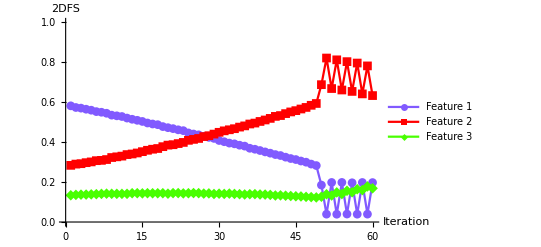

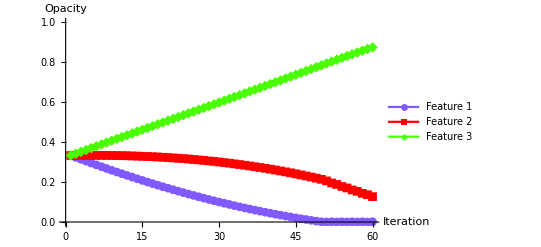

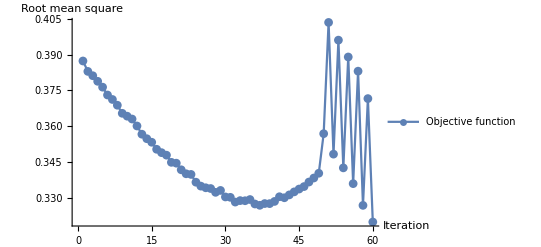

```mathematica
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","2DFS"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_saliency_2dfs.pdf",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","Opacity"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_opacity_2dfs.pdf",opacity1];
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->None,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iteration","Root mean square"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_rms_2dfs.pdf",rms1];
rmslist1=#3&@@@list;
path1=#2&@@@list;
minstep1=First@FirstPosition[rmslist1,_?(#==Min[rmslist1]&)];
```

```mathematica
rgba1=Transpose[Append[rgb1,alpha1]]//(RGBColor/@#&);
rgbafunction1=(Blend[Transpose[{intensity,rgba1}], #1] & );
imgs=Image3D[#,ColorFunction->rgbafunction1,ViewPoint->viewpoints[face]]&/@Prepend[ImageMultiply[d,#]&/@features,d]//Image@Rasterize[#]&/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
path1[[-1]]
Last@path1
```

{0.00121051,0.127156,0.875228}

{0.00121051,0.127156,0.875228}

```mathematica
Export[StringReplace[imagefile,"."->"_optimized_2dfs."],First@imgs];
MapIndexed[Export[StringReplace[imagefile,"."->"_optimized_2dfs_"<>ToString[First[#2]]<>"."],#]&,imgs[[2;;]]];
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xmlobject},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xmlobject=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function created using Wolfram Mathematica"]},VoreenData,{}];
Export[filename,xmlobject, "XML"];
rgbafunction2
];
```

```mathematica
intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];
tf1=saveTransferFunction[path1[[minstep1]],plotpath<>dataname<>"_optimized_2dfs.tfi"];
```